```mathematica
objective=3x+2y
```

3 x+2 y

```mathematica
constraints=2x+3y≤24&&3x+5y≤40&&7x+2y≤70&&x-y≤9&&x≥0&&y≥0
```

2 x+3 y≤24&&3 x+5 y≤40&&7 x+2 y≤70&&x-y≤9&&x≥0&&y≥0

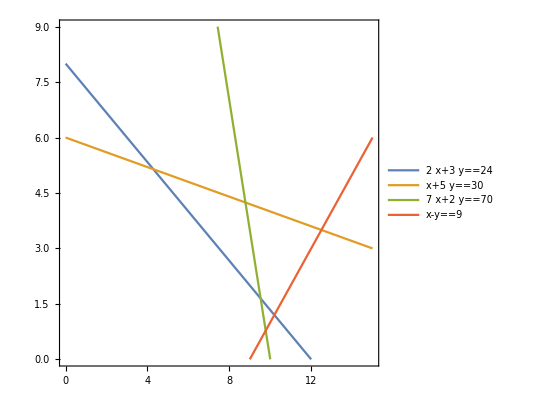

```mathematica
ContourPlot[{2x+3y==24,x+5y==30,7x+2y==70,x-y==9},{x,0,15},{y,0,9},PlotLegends->"Expressions"]
```

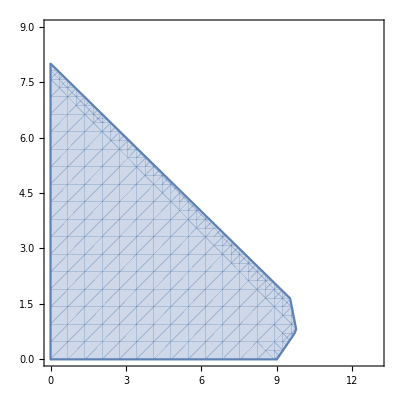

```mathematica
feasibleregion=RegionPlot[constraints,{x,0,13},{y,0,9}]
```

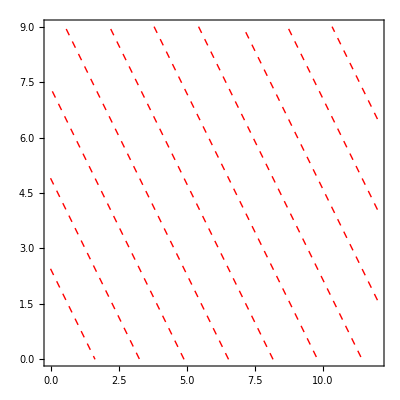

```mathematica
objectivecontours=ContourPlot[objective,{x,0,12},{y,0,9},ContourShading->None,ContourStyle->Directive[Red,Dashed,Thick],Contours->10]
```

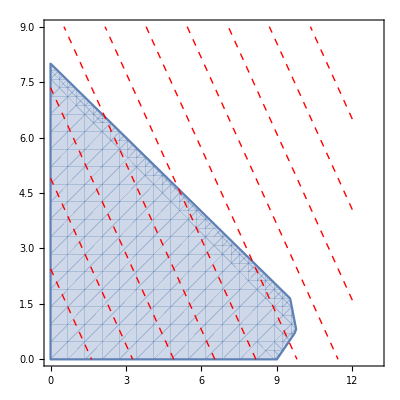

```mathematica
Show[feasibleregion,objectivecontours]
```

```mathematica
Manipulate[
Show[feasibleregion,
ContourPlot[objective==c,{x,0,12},{y,0,9},ContourShading->None,ContourStyle->Directive[Red,Dashed,Thick],Contours->10]],
{c,0,100}]
```

```mathematica
Maximize[{objective,constraints},{x,y}]
```

{542/17,{x→162/17,y→28/17}}

```mathematica
N[%]
```

{31.8824,{x→9.52941,y→1.64706}}

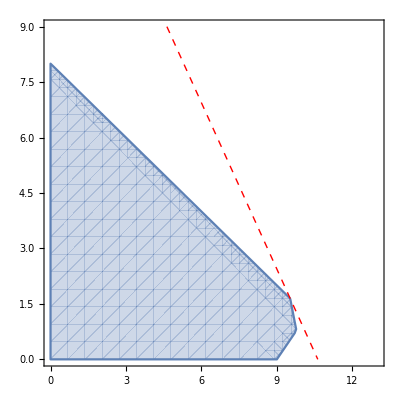

```mathematica
Show[feasibleregion,
ContourPlot[objective==31.8824,{x,0,12},{y,0,9},ContourShading->None,ContourStyle->Directive[Red,Dashed,Thick]]]
```